```mathematica
(*I^2 / V*)
(*Import and organize data*)
dataset2 = Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/7_Lab/t2.csv"];
```

0.00372278+0.00941007 x

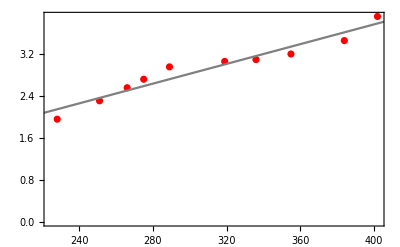
-Graphics-Current.b2 (A.b2)Accleration Voltage(V)

```mathematica
col1 = dataset2[[All, 1]][[2 ;; 11]]; (*Potential*)
col2 = dataset2[[All, 2]][[2 ;; 11]];(*Current (A)*)
col3 = dataset2[[All, 3]][[2 ;; 11]];(*Current^2 (A)^2*)
col4 = dataset2[[All, 4]][[2 ;; 11]];(*Predicted (A)^2*)
col5 = dataset2[[All, 5]][[2 ;; 11]];(*Residual*)
col6 = dataset2[[All, 6]][[2 ;; 11]];(*Uncertainty (A)*)
col7 = dataset2[[All, 7]][[2 ;; 11]];(*Uncertainty (A^2)*)

(*Display table*)
TableForm[dataset2];

(*Pair Data*)
dataInterpolate2 = {col1, col3};
dataBund2 = Transpose[dataInterpolate2];

(*Graph Data*)
ListPlot[dataBund2,PlotMarkers->{"o",Large}];

(*Least Squares Fit*)
lm = LinearModelFit[dataBund2, x, x];
Normal@lm  (*Print out line of least squares fit*)

l7 = Labeled[
Show[
ListPlot[dataBund2, PlotStyle->Red],
Plot[lm[x],{x,0,1000}, PlotStyle->Gray], (*Take note of bounds*)
Frame->True], 
{"Current.b2 (A.b2)", "Accleration Voltage(V)"},
{Left, Bottom},
RotateLabel->True
]
```

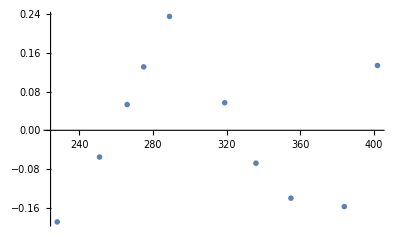

```mathematica
(*-------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------*)

(*Residuals*)

(*Pair Data*)
dataInteropResidual2 = {col1, col5};
dataBundleResidual2 = Transpose[dataInteropResidual2];

(*Graph Data*)
ListPlot[dataBundleResidual2,PlotMarkers->{"o",Large}]
```

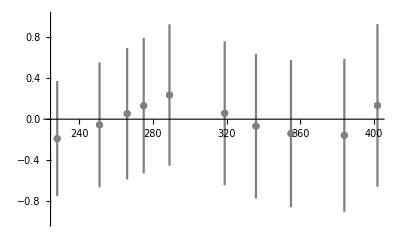
-Graphics-square of current residuals (A.b2)Acceleration Voltage (V)

```mathematica
(*Pair Data with Uncertainty*)
dataW2Uncertainty = {col1, col5, col7}; (*potential, residuals, uncertainty (A^2)*)
dataBundleW2Uncertainty = Transpose[dataW2Uncertainty];


(*Error Bars work, they are just really small*)
Needs["ErrorBarPlots`"]
l8 = Labeled[
	Show[
	ListPlot[dataBundleResidual2, PlotRange->{-1, 1}],     (*Note the Range*)
	ErrorListPlot[dataBundleW2Uncertainty,PlotStyle->Gray]
   ],
{"square of current residuals (A.b2)", "Acceleration Voltage (V)"},
{Left, Bottom},
RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"graph_7.png", l7, ImageResolution-> 200]
Export[NotebookDirectory[]<>"graph_residual7.png", l8, ImageResolution-> 200]
```

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/7_Lab/graph_7.png

/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/Labs/7_Lab/graph_residual7.png